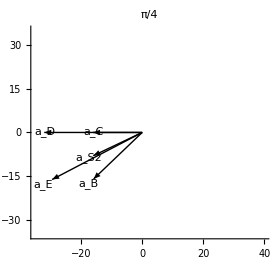
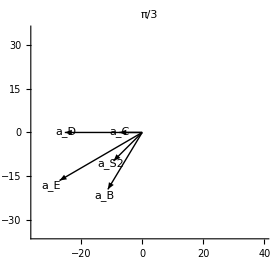
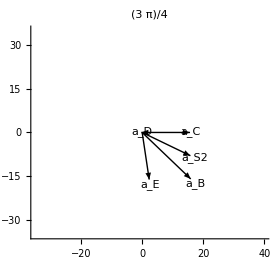
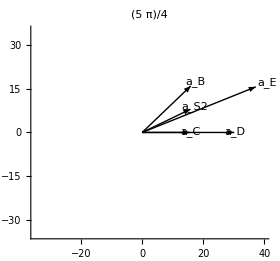
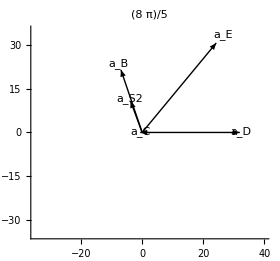
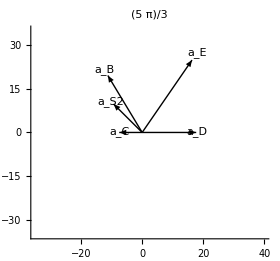

```mathematica
Row[Graphics[{Text["a_B",Subscript[a, B][x]+0.1 Subscript[a, B][x]],Text["a_C",Subscript[a, C][x]+0.2],Text["a_D",Subscript[a, D][x]+0.2],Text["a_E",Subscript[a, E][x]+0.1 Subscript[a, E][x]],Text["a_S2",Subscript[a, S2][x]+0.1 Subscript[a, S2][x]], , Arrow[{{0,0},#}]&/@{Subscript[a, B][x],Subscript[a, C][x],Subscript[a, D][x],Subscript[a, E][x],Subscript[a, S2][x]}},Axes->True,PlotRange->{{-35,40},{-35,35}},ImageSize->280 ,PlotLabel->x ]/.x-># &/@{Pi/4,Pi/3,3Pi/4,5Pi/4,8Pi/5,10Pi/6}]
```